# Scalar Phi34

```mathematica
NotebookDirectory[]
```

/home/raj/C_SM/SM/

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$model="Phi34";
```

```mathematica
<<GenAmp`
```

## Setup

```mathematica
$gaugerules={FAGaugeXi[S[1]]:> 1};
```

```mathematica
$ampconfigFCFAConvert={ChangeDimension->D,Contract->False,DropSumOver->False,FCFADiracChainJoin->True,FeynAmpDenominatorCombine->True,
FinalSubstitutions->{},InitialSubstitutions->{},List->False,LoopMomenta->{l},LorentzIndexNames->{},Prefactor->1,SMP->False,SUNFIndexNames->{},
SUNIndexNames->{},TransversePolarizationVectors->{},UndoChiralSplittings->False};
```

## Tree Level (2->2)

loading generic model file /home/raj/C_SM/SM/models/Phi34/Phi34.gen

> $GenericMixing is OFF

generic model {./models/Phi34/Phi34} initialized

loading classes model file /home/raj/C_SM/SM/models/Phi34/Phi34.mod

> 1 particles (incl. antiparticles) in 1 classes

> $CounterTerms are ON

> 2 vertices

> 4 counterterms of order 1

classes model {./models/Phi34/Phi34} initialized

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 1 Particles insertion

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 4 Particles insertions

in total: 0 Particles insertions

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebf/cedf/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams

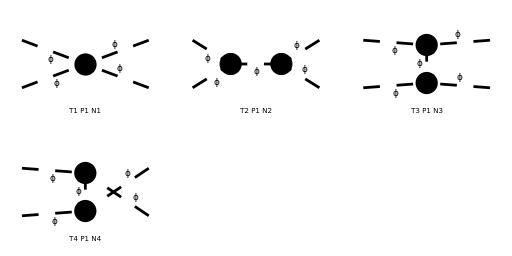

```mathematica
DTPPPP=diag[0,{S[1],S[1]},{S[1],S[1]}];
```

```mathematica
AmpTPPPP=FCFAConvert[CreateFeynAmp[#,GaugeRules->$gaugerules],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},ChangeDimension->4,List->False]&/@DTPPPP//Total
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

> Top. 4: 1 Particles amplitude

in total: 4 Particles amplitudes

creating amplitudes at level(s) {Particles}

in total: 0 Particles amplitudes

-g3^2/((OverBar[k1]+OverBar[k2])^2-mP^2)-g3^2/((OverBar[k1]-OverBar[p2])^2-mP^2)-g3^2/((OverBar[k2]-OverBar[p2])^2-mP^2)-g4

```mathematica
(*FCClearScalarProducts[];
SetMandelstam[s,t,u,p1t,p2t,-k1t,-k2t,mP,mP,mP,mP];*)
```

```mathematica
(*AmpT22SQEDSSSS1=FeynAmpDenominatorExplicit[AmpTPPPP]//FullSimplify*)
```

## Tadpoles (1->0)

## One Loop P->0

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ab/0/bb.m, 0 diagrams

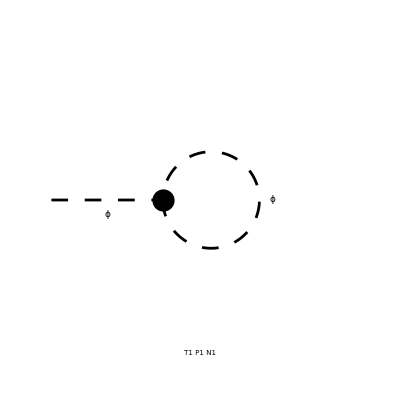

> Top. 1 ab/0/0.m, 0 diagrams

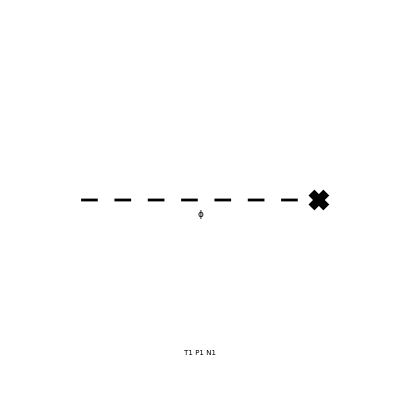

```mathematica
D1LP=diag[1,{S[1]},{}];
```

```mathematica
Amp1LP=D1LP//amp1L[{p1},{}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

Part::partw: Part 2 of {} does not exist.

{-(ⅈ g3)/(32 π^4 (l^2-mP^2)),-dv mP^2 √ZP}

```mathematica
Amp1LPDiv=Amp1LP//amp1LSimplify[{dv->Nd*dv,ZP-> 1+Nd*dP},{SMP["Delta"],dv,dP}]
```

(Δ g3 mP^2)/(16 π^2)-dv mP^2

```mathematica
dsol[0]=Solve[SelectFree2[Amp1LPDiv,p1]==0,dv]//Flatten//Simplify
dSave[dsol[0]];
```

{dv→(Δ g3)/(16 π^2)}

## One Loop (1->1)

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 1 Particles insertion

in total: 2 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ac/bc/cc.m, 0 diagrams

> Top. 2 ac/bd/cdcd.m, 0 diagrams

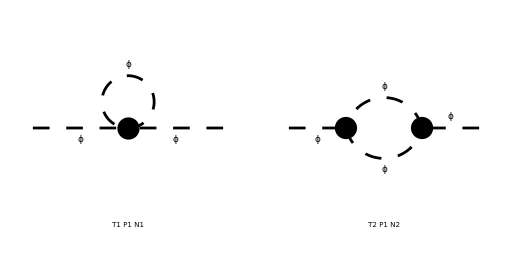

> Top. 1 ac/bc/0.m, 0 diagrams

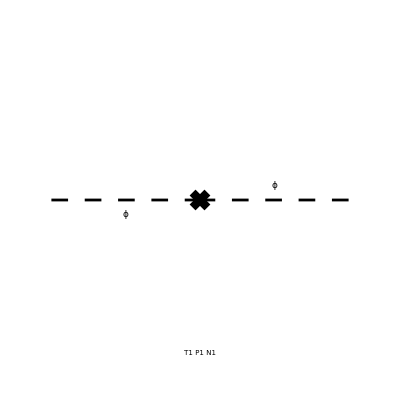

```mathematica
D1LPP=diag[1,{S[1]},{S[1]}];
```

```mathematica
Amp1LPP=D1LPP//amp1L[{p1},{p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

in total: 2 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ g3^2)/(32 π^4 (l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ g4)/(32 π^4 (l^2-mP^2)),-ⅈ (ⅈ p1^2 (ZP-1)-ⅈ (dv g3 ZP^2+mP^2 ZmP^2 ZP-mP^2))}

```mathematica
Amp1LPPDiv=Amp1LPP//amp1LSimplify[{ZP->1+Nd*dP,ZmP->1+Nd*dmP},{SMP["Delta"],dmP,dP,dv}]
```

-2 dmP mP^2-2 dP dv g3-dP mP^2+dP p1^2-dv g3+(Δ (g3^2+g4 mP^2))/(16 π^2)

```mathematica
dsol[1]=Solve[SelectNotFree2[Amp1LPPDiv,p1]==0,dP]//Flatten//Simplify
dSave[dsol[1]];
```

{dP→0}

```mathematica
dsol[2]=Solve[SelectFree2[Amp1LPPDiv/.dSub[dmP],p1]==0,dmP]//Flatten//Simplify
dSave[dsol[2]];
```

{dmP→(Δ g4)/(32 π^2)}

## One Loop (2->1)

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 1 Particles insertion

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 4 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 adbe/cf/dedfef.m, 0 diagrams

> Top. 2 adbe/ce/dede.m, 0 diagrams

> Top. 3 adbe/cd/eded.m, 0 diagrams

> Top. 4 adbd/ce/eded.m, 0 diagrams

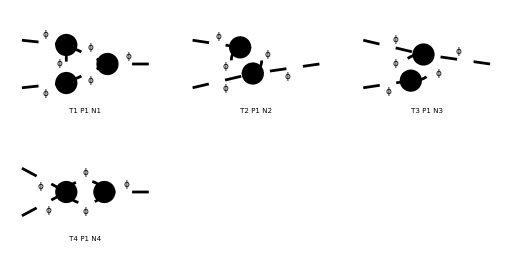

> Top. 1 adbd/cd/0.m, 0 diagrams

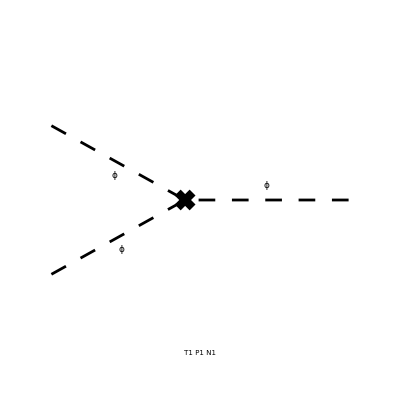

```mathematica
D1LPPP=diag[1,{S[1],S[1]},{S[1]}];
```

```mathematica
Amp1LPPP=D1LPPP//amp1L[{p1,p1},{2p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

> Top. 4: 1 Particles amplitude

in total: 4 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ g3^3)/(16 π^4 (l^2-mP^2).((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ g3 g4)/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ g3 g4)/(32 π^4 (l^2-mP^2).((l+2 p1)^2-mP^2)),-dv g4 ZP^(3/2)-g3 Zg3 ZP^(3/2)+g3}

```mathematica
Amp1LPPPDiv=Amp1LPPP//amp1LSimplify[{ZP->1+Nd*dP,Zg3->1+Nd*dg3},{SMP["Delta"],dP,dg3,dv}]
```

-dg3 g3-(3 dP dv g4)/2-(3 dP g3)/2-dv g4+(3 Δ g3 g4)/(16 π^2)

```mathematica
dsol[3]=Simplify[Flatten[Solve[SelectFree2[Amp1LPPPDiv/.dSub[dg3],p]==0,dg3]]]
dSave[dsol[3]];
```

{dg3→(Δ g4)/(8 π^2)}

## One Loop (2->2)

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

> Top. 2: 1 Particles insertion

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

> Top. 5: 1 Particles insertion

> Top. 6: 1 Particles insertion

> Top. 7: 1 Particles insertion

> Top. 8: 1 Particles insertion

> Top. 9: 1 Particles insertion

> Top. 10: 1 Particles insertion

> Top. 11: 1 Particles insertion

> Top. 12: 1 Particles insertion

in total: 12 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 aebf/cgdg/efegfg.m, 0 diagrams

> Top. 2 aebf/cgdf/egefgf.m, 0 diagrams

> Top. 3 aebf/cfdg/egefgf.m, 0 diagrams

> Top. 4 aebf/cgde/fgfege.m, 0 diagrams

> Top. 5 aebf/cedg/fgfege.m, 0 diagrams

> Top. 6 aebe/cfdg/fgfege.m, 0 diagrams

> Top. 7 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 8 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 9 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 10 aebe/cfdf/efef.m, 0 diagrams

> Top. 11 aebf/cedf/efef.m, 0 diagrams

> Top. 12 aebf/cfde/efef.m, 0 diagrams

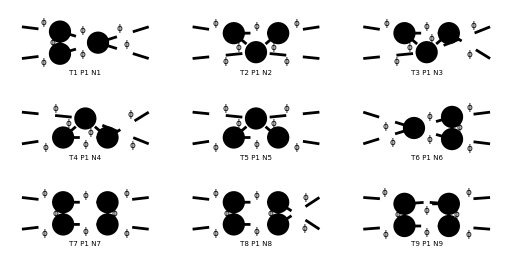

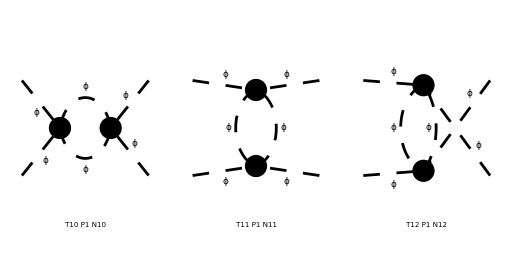

> Top. 1 aebe/cede/0.m, 0 diagrams

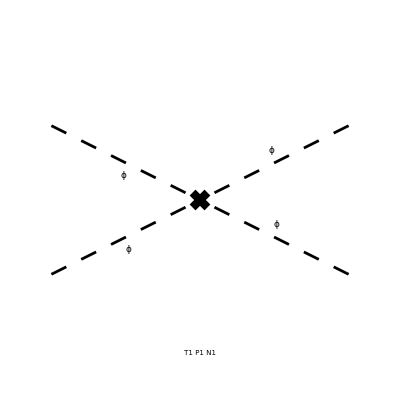

```mathematica
D1LPPPP=diag[1,{S[1],S[1]},{S[1],S[1]}];
```

```mathematica
Amp1LPPPP=D1LPPPP//amp1L[{p1,p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

> Top. 4: 1 Particles amplitude

> Top. 5: 1 Particles amplitude

> Top. 6: 1 Particles amplitude

> Top. 7: 1 Particles amplitude

> Top. 8: 1 Particles amplitude

> Top. 9: 1 Particles amplitude

> Top. 10: 1 Particles amplitude

> Top. 11: 1 Particles amplitude

> Top. 12: 1 Particles amplitude

in total: 12 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ g3^4)/(16 π^4 (l^2-mP^2).((l-p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ g3^4)/(8 π^4 (l^2-mP^2).((l+p1)^2-mP^2).(l^2-mP^2).((l-p1)^2-mP^2))-(ⅈ g3^2 g4)/(4 π^4 (l^2-mP^2).((l-p1)^2-mP^2)^2)-(ⅈ g3^2 g4)/(8 π^4 (l^2-mP^2).((l+p1)^2-mP^2).((l-p1)^2-mP^2))-(ⅈ g4^2)/(32 π^4 (l^2-mP^2).((l-2 p1)^2-mP^2))-(ⅈ g4^2)/(16 π^4 (l^2-mP^2)^2),-g4 (Zg4 ZP^2-1)}

```mathematica
Amp1LPPPPDiv=Amp1LPPPP//amp1LSimplify[{ZP->1+Nd*dP,Zg4->1+Nd*dg4},{SMP["Delta"],dP,dg4}]
```

-dg4 g4-2 dP g4+(3 Δ g4^2)/(16 π^2)

```mathematica
dsol[4]=Simplify[Flatten[Solve[SelectFree2[Amp1LPPPPDiv/.dSub[dg4],p]==0/.dsol[1],dg4]]]
dSave[dsol[4]];
```

{dg4→(3 Δ g4)/(16 π^2)}

## Final answers

```mathematica
dvalues
```

{dv→(Δ g3)/(16 π^2),dP→0,dmP→(Δ g4)/(32 π^2),dg3→(Δ g4)/(8 π^2),dg4→(3 Δ g4)/(16 π^2)}